```mathematica
$Assumptions={A1>0,B1>0,A2>0,B2>0,A>0,B>0,};

(*A1=A;A2=A;B1=B;B2=B;*)

W={{-A1-B2,A2+B1 ⅇ^(ⅈ k)},{A1+B2/ⅇ^(ⅈ k),-A2-B1}};
λ=Eigenvalues[W];
R=Transpose[Eigenvectors[W]];(*Columns of R are right eigenvectors*)
L=Inverse[R];(*Rows of L are left eigenvectors*)
ψ0={1,0};
g[k_,x_] = {1,1}. Transpose[R][[1]] * ψ0.L[[1]]*Exp[λ[[1]]/x]+ {1,1}. Transpose[R][[2]] * ψ0.L[[2]]*Exp[λ[[2]]/x];
x1[k_,x_]=-ⅈ*D[g[k,x],k];
x2[k_,x_]=-D[D[g[k,x],k],k];
```

```mathematica
l1[k_,A1_,A2_,B1_,B2_]=D[λ[[2]],k];
l2[k_,A1_,A2_,B1_,B2_]=D[D[λ[[2]],k],k];
```

```mathematica
l1[0,A1,A2,B1,B2]
```

-1/2 ⅈ (-A1-A2-B1-B2+√((A1+A2+B1+B2)^2))+1/2 (-ⅈ A1-ⅈ A2-ⅈ B1-ⅈ B2+(2 (ⅈ A1+ⅈ A2+ⅈ B1+ⅈ B2) (A1+A2+B1+B2)-4 (-ⅈ A1 B1+ⅈ A2 B2))/(2 √((A1+A2+B1+B2)^2)))

```mathematica
Simplify[-1/2 ⅈ (-A1-A2-B1-B2+√((A1+A2+B1+B2)^2))+1/2 (-ⅈ A1-ⅈ A2-ⅈ B1-ⅈ B2+(2 (ⅈ A1+ⅈ A2+ⅈ B1+ⅈ B2) (A1+A2+B1+B2)-4 (-ⅈ A1 B1+ⅈ A2 B2))/(2 √((A1+A2+B1+B2)^2)))]
```

(ⅈ (A1 B1-A2 B2))/(A1+A2+B1+B2)

```mathematica
Simplify[-1/2 ⅈ (-A1-A2-B1-B2-√((A1+A2+B1+B2)^2))+1/2 (-ⅈ A1-ⅈ A2-ⅈ B1-ⅈ B2-(2 (ⅈ A1+ⅈ A2+ⅈ B1+ⅈ B2) (A1+A2+B1+B2)-4 (-ⅈ A1 B1+ⅈ A2 B2))/(2 √((A1+A2+B1+B2)^2)))]
```

-(ⅈ (A1 B1-A2 B2))/(A1+A2+B1+B2)

```mathematica
Simplify[-1/2 ⅈ (-A1-A2-B1-B2+√((A1+A2+B1+B2)^2))+1/2 (-ⅈ A1-ⅈ A2-ⅈ B1-ⅈ B2+(2 (ⅈ A1+ⅈ A2+ⅈ B1+ⅈ B2) (A1+A2+B1+B2)-4 (-ⅈ A1 B1+ⅈ A2 B2))/(2 √((A1+A2+B1+B2)^2)))]
```

(ⅈ (A1 B1-A2 B2))/(A1+A2+B1+B2)

```mathematica
Simplify[%92]
```

(ⅈ (-A2 B2+A1 B1 ⅇ^(2 ⅈ k)))/(√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))

```mathematica
FullSimplify[λ]
```

{1/2 ⅇ^(-ⅈ k) (-(A1+A2+B1+B2) ⅇ^(ⅈ k)-√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k)))),1/2 ⅇ^(-ⅈ k) (-(A1+A2+B1+B2) ⅇ^(ⅈ k)+√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))}

```mathematica
Simplify[D[λ[[2]],k]]
```

(ⅈ (-A2 B2+A1 B1 ⅇ^(2 ⅈ k)))/(√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))

```mathematica
Normal[FullSimplify[Series[λ[[2]],{k,0,2}]]]
```

(ⅈ (A1 B1-A2 B2) k)/(A1+A2+B1+B2)-((A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))) k^2)/(2 (A1+A2+B1+B2)^3)

```mathematica
1/2 ⅇ^(-ⅈ k) (-γ ⅇ^(ⅈ k)+√(γ^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))
```

1/2 ⅇ^(-ⅈ k) (-ⅇ^(ⅈ k) γ+√(4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))+ⅇ^(2 ⅈ k) γ^2))

```mathematica
Assuming[γ>0,Simplify[Series[1/2 ⅇ^(-ⅈ k) (-ⅇ^(ⅈ k) γ+√(4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))+ⅇ^(2 ⅈ k) γ^2)),{k,0,2}]]]
```

(ⅈ (A1 B1-A2 B2) k)/γ+((2 A1^2 B1^2+A2 B2 (2 A2 B2-γ^2)-A1 B1 (4 A2 B2+γ^2)) k^2)/(2 γ^3)+O[k]^3

```mathematica
Normal[FullSimplify[Series[λ[[1]],{k,0,2}]]]
```

-A1-A2-B1-B2+(ⅈ (-A1 B1+A2 B2) k)/(A1+A2+B1+B2)+((A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))) k^2)/(2 (A1+A2+B1+B2)^3)

```mathematica
Simplify[1/2 ⅇ^(-ⅈ k) (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)+√((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k))))]
```

-1/2 ⅇ^(-ⅈ k) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k)-√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))

```mathematica
FullSimplify[1/2 ⅇ^(-ⅈ k) (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)+√((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k))))]
```

1/2 ⅇ^(-ⅈ k) (-(A1+A2+B1+B2) ⅇ^(ⅈ k)+√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))

```mathematica
FullSimplify[1/2 ⅇ^(-ⅈ k) (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)+√((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k))))]
```

1/2 ⅇ^(-ⅈ k) (-(A1+A2+B1+B2) ⅇ^(ⅈ k)+√((A1+A2+B1+B2)^2 ⅇ^(2 ⅈ k)+4 ⅇ^(ⅈ k) (-1+ⅇ^(ⅈ k)) (-A2 B2+A1 B1 ⅇ^(ⅈ k))))

```mathematica
Normal[Simplify[Series[λ[[2]],{k,0,2}]]]
```

(ⅈ (A1 B1-A2 B2) k)/(A1+A2+B1+B2)-((A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))) k^2)/(2 (A1+A2+B1+B2)^3)

```mathematica
a=5;b=2;s2=s-s1;s1=1;
A1=a*Exp[s1/2];A2=a*Exp[-s1/2];B1=b*Exp[s2/2];B2=b*Exp[-s2/2];
```

```mathematica
Series[ⅈ*l1[0,A1,A2,B1,B2]/l2[0,A1,A2,B1,B2],{s,0,2}]
```

```mathematica
N[((-1+ⅇ) (5+4 √ⅇ+5 ⅇ)^2)/(25+20 √ⅇ+91 ⅇ+120 ⅇ^(3/2)+91 ⅇ^2+20 ⅇ^(5/2)+25 ⅇ^3)+(2 (5+4 √ⅇ+5 ⅇ)^2 (5 √ⅇ+25 ⅇ+35 ⅇ^(3/2)+66 ⅇ^2+35 ⅇ^(5/2)+25 ⅇ^3+5 ⅇ^(7/2)) s)/((25+20 √ⅇ+91 ⅇ+120 ⅇ^(3/2)+91 ⅇ^2+20 ⅇ^(5/2)+25 ⅇ^3)^2)+((-3125 √ⅇ+23750 ⅇ+60750 ⅇ^(3/2)+197150 ⅇ^2+339530 ⅇ^(5/2)+540150 ⅇ^3+509910 ⅇ^(7/2)+349342 ⅇ^4-349342 ⅇ^5-509910 ⅇ^(11/2)-540150 ⅇ^6-339530 ⅇ^(13/2)-197150 ⅇ^7-60750 ⅇ^(15/2)-23750 ⅇ^8+3125 ⅇ^(17/2)) s^2)/(2 (25+20 √ⅇ+91 ⅇ+120 ⅇ^(3/2)+91 ⅇ^2+20 ⅇ^(5/2)+25 ⅇ^3)^3)+O[s]^3]
```

0.482013+0.450265 (s+0.)-0.0410387 (s+0.)^2+O[s+0.]^3

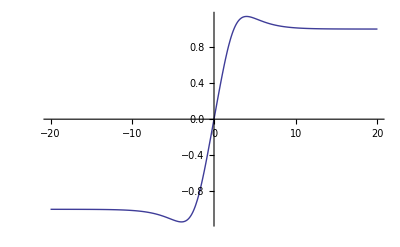

```mathematica
Plot[ⅈ l1[0,A1,A2,B1,B2]/l2[0,A1,A2,B1,B2],{s,-20,20},PlotRange->Full]
```

```mathematica
s=5;
N[Λ[10^{-3}]]
```

{-3.79451×10^-7+0.000848284 ⅈ}

```mathematica
Chop[{-2.499999949167933*^-7-2.1442863432483768*^-19 ⅈ}]
```

{-2.5×10^-7}

```mathematica
Λ[0]
```

0

```mathematica
D[λ[[2]],k]
```

-1/2 ⅈ ⅇ^(-ⅈ k) (-2 ⅇ^(ⅈ k)-ⅇ^(ⅈ k-s/2)-ⅇ^(ⅈ k+s/2)+√((2 ⅇ^(ⅈ k)+ⅇ^(ⅈ k-s/2)+ⅇ^(ⅈ k+s/2))^2-4 (-ⅇ^(ⅈ k-s/2)+ⅇ^(2 ⅈ k-s/2)+ⅇ^(2 ⅈ k+s/2)-ⅇ^(3 ⅈ k+s/2))))+1/2 ⅇ^(-ⅈ k) (-2 ⅈ ⅇ^(ⅈ k)-ⅈ ⅇ^(ⅈ k-s/2)-ⅈ ⅇ^(ⅈ k+s/2)+(2 (2 ⅈ ⅇ^(ⅈ k)+ⅈ ⅇ^(ⅈ k-s/2)+ⅈ ⅇ^(ⅈ k+s/2)) (2 ⅇ^(ⅈ k)+ⅇ^(ⅈ k-s/2)+ⅇ^(ⅈ k+s/2))-4 (-ⅈ ⅇ^(ⅈ k-s/2)+2 ⅈ ⅇ^(2 ⅈ k-s/2)+2 ⅈ ⅇ^(2 ⅈ k+s/2)-3 ⅈ ⅇ^(3 ⅈ k+s/2)))/(2 √((2 ⅇ^(ⅈ k)+ⅇ^(ⅈ k-s/2)+ⅇ^(ⅈ k+s/2))^2-4 (-ⅇ^(ⅈ k-s/2)+ⅇ^(2 ⅈ k-s/2)+ⅇ^(2 ⅈ k+s/2)-ⅇ^(3 ⅈ k+s/2)))))

```mathematica
Simplify[%16]
```

(ⅈ ⅇ^(-s/2) (-1+ⅇ^(2 ⅈ k+s)))/(√(6 ⅇ^(2 ⅈ k)+ⅇ^(2 ⅈ k-s)+4 ⅇ^(ⅈ k-s/2)+4 ⅇ^(3 ⅈ k+s/2)+ⅇ^(2 ⅈ k+s)))

```mathematica
s=0
```

0

```mathematica
N[W]
```

```mathematica
MatrixForm[W]
```

(-2 | 1+ⅇ^(ⅈ k)
1+ⅇ^(-ⅈ k) | -2)

```mathematica
Simplify[Eigenvalues[W]]
```

{-3.9975,-0.00249948}

```mathematica
l1[k,a1,a2,b1,b2]
```

(ⅈ (-1+ⅇ^(2 ⅈ k)))/(2 √(ⅇ^(ⅈ k) (1+ⅇ^(ⅈ k))^2))

```mathematica
N[l1[0,A1,A2,B1,B2]]
```

0.

```mathematica
N[l1[0,A1,A2,B1,B2],20]
```

0

```mathematica
k=0.1
```

0.1

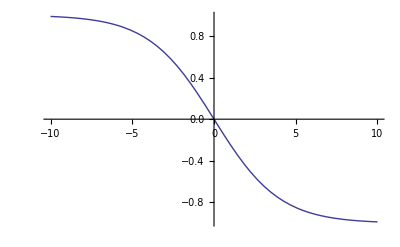

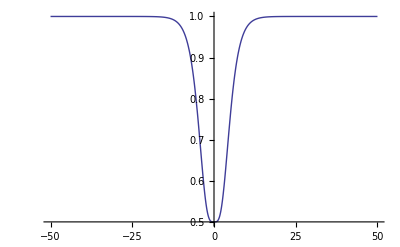

```mathematica
Plot[ⅈ*l1[0,A1,A2,B1,B2],{s,-10,10}]
Plot[-l2[0,A1,A2,B1,B2],{s,-50,50},PlotRange->Full]
```

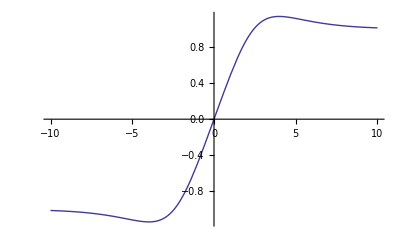

```mathematica
Plot[ⅈ*l1[0,A1,A2,B1,B2]/l2[0,A1,A2,B1,B2],{s,-10,10}]
```

```mathematica
Plot[((-1+ⅇ^(s/2)) (1+ⅇ^(s/2))^3)/(1+6 ⅇ^s+ⅇ^(2 s)),{{s,ConditionalExpression[1/2 (Abs[Min[-2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (1.1150304598998477+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (1.1150304598998477+Re[(0.+6.283185307179586 ⅈ) C[1]])]]+Abs[Min[-2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (2.4454088190556567+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (2.4454088190556567+Re[(0.+6.283185307179586 ⅈ) C[1]])]]),C[1]∈Integers],ConditionalExpression[1/2 (-Abs[Min[-2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (3.472572236488591+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (3.472572236488591+Re[(0.+6.283185307179586 ⅈ) C[1]])]]-Abs[Min[-2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (3.706353773815326+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (3.706353773815326+Re[(0.+6.283185307179586 ⅈ) C[1]])]]),C[1]∈Integers]},CalculateUtilities`SuggestPlotRanges`Private`PRData[CalculateUtilities`SuggestPlotRanges`Private`enlargePlotRange[{{ConditionalExpression[1/2 (Abs[Min[-2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (1.1150304598998477+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (1.1150304598998477+Re[(0.+6.283185307179586 ⅈ) C[1]])]]+Abs[Min[-2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (2.4454088190556567+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (2.4454088190556567+Re[(0.+6.283185307179586 ⅈ) C[1]])]]),C[1]∈Integers],ConditionalExpression[1/2 (-Abs[Min[-2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (3.472572236488591+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. (3.141592653589793+Im[(0.+6.283185307179586 ⅈ) C[1]])+2. (3.472572236488591+Re[(0.+6.283185307179586 ⅈ) C[1]])]]-Abs[Min[-2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (3.706353773815326+Re[(0.+6.283185307179586 ⅈ) C[1]]),2. Im[(0.+6.283185307179586 ⅈ) C[1]]+2. (3.706353773815326+Re[(0.+6.283185307179586 ⅈ) C[1]])]]),C[1]∈Integers]}},2],"HorizontalPlotRangeType"->"ShowGlobalShape"]}]
```

Plot::pllim: Range specification {{s, ConditionalExpression[1/2\ (Abs[Min[Plus[« 2 »], Plus[« 2 »]]] + Abs[Min[Plus[« 2 »], Plus[« 2 »]]]), C[1] ∈ Integers], ConditionalExpression[1/2\ (-Abs[Min[« 2 »]] - Abs[Min[« 2 »]]), C[1] ∈ Integers]}, CalculateUtilities`SuggestPlotRanges`Private`PRData[CalculateUtilities`SuggestPlotRanges`Private`enlargePlotRange[{{ConditionalExpression[« 2 »\ Plus[« 2 »], C[« 1 »] ∈ Integers], ConditionalExpression[« 2 »\ Plus[« 2 »], C[« 1 »] ∈ Integers]}}, 2], "HorizontalPlotRangeType" → "ShowGlobalShape"]} is not of the form {x, xmin, xmax}.

Plot[((-1+ⅇ^(s/2)) (1+ⅇ^(s/2))^3)/(1+6 ⅇ^s+ⅇ^(2 s)),{{s,ConditionalExpression[1/2 (Abs[Min[-2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (1.11503+Re[(0.+6.28319 ⅈ) C[1]]),2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (1.11503+Re[(0.+6.28319 ⅈ) C[1]])]]+Abs[Min[-2. Im[(0.+6.28319 ⅈ) C[1]]+2. (2.44541+Re[(0.+6.28319 ⅈ) C[1]]),2. Im[(0.+6.28319 ⅈ) C[1]]+2. (2.44541+Re[(0.+6.28319 ⅈ) C[1]])]]),C[1]∈Integers],ConditionalExpression[1/2 (-Abs[Min[-2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (3.47257+Re[(0.+6.28319 ⅈ) C[1]]),2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (3.47257+Re[(0.+6.28319 ⅈ) C[1]])]]-Abs[Min[-2. Im[(0.+6.28319 ⅈ) C[1]]+2. (3.70635+Re[(0.+6.28319 ⅈ) C[1]]),2. Im[(0.+6.28319 ⅈ) C[1]]+2. (3.70635+Re[(0.+6.28319 ⅈ) C[1]])]]),C[1]∈Integers]},CalculateUtilities`SuggestPlotRanges`Private`PRData[CalculateUtilities`SuggestPlotRanges`Private`enlargePlotRange[{{ConditionalExpression[1/2 (Abs[Min[-2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (1.11503+Re[(0.+6.28319 ⅈ) C[1]]),2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (1.11503+Re[(0.+6.28319 ⅈ) C[1]])]]+Abs[Min[-2. Im[(0.+6.28319 ⅈ) C[1]]+2. (2.44541+Re[(0.+6.28319 ⅈ) C[1]]),2. Im[(0.+6.28319 ⅈ) C[1]]+2. (2.44541+Re[(0.+6.28319 ⅈ) C[1]])]]),C[1]∈Integers],ConditionalExpression[1/2 (-Abs[Min[-2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (3.47257+Re[(0.+6.28319 ⅈ) C[1]]),2. (3.14159+Im[(0.+6.28319 ⅈ) C[1]])+2. (3.47257+Re[(0.+6.28319 ⅈ) C[1]])]]-Abs[Min[-2. Im[(0.+6.28319 ⅈ) C[1]]+2. (3.70635+Re[(0.+6.28319 ⅈ) C[1]]),2. Im[(0.+6.28319 ⅈ) C[1]]+2. (3.70635+Re[(0.+6.28319 ⅈ) C[1]])]]),C[1]∈Integers]}},2],HorizontalPlotRangeType→ShowGlobalShape]}]

```mathematica
Simplify[(ⅈ ⅇ^(-1/2-s2/2) (-1+ⅇ^(1+s2)))/(√(ⅇ^(-1-s2) (√ⅇ+ⅇ^(1+s2/2)+ⅇ^(s2/2)+ⅇ^(1/2+s2))^2))]
```

(ⅈ ⅇ^(-1/2-s2/2) (-1+ⅇ^(1+s2)))/(√(ⅇ^(-1-s2) (√ⅇ+ⅇ^(1+s2/2)+ⅇ^(s2/2)+ⅇ^(1/2+s2))^2))

```mathematica
l2[0]
```

1/2 (1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2)-√((1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2))^2))-ⅈ (-ⅈ/(√ⅇ)-ⅈ √ⅇ-ⅈ ⅇ^(-s2/2)-ⅈ ⅇ^(s2/2)+(-4 (ⅈ ⅇ^(-1/2-s2/2)-ⅈ ⅇ^(1/2+s2/2))+2 (ⅈ/(√ⅇ)+ⅈ √ⅇ+ⅈ ⅇ^(-s2/2)+ⅈ ⅇ^(s2/2)) (1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2)))/(2 √((1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2))^2)))+1/2 (1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2)+(-4 (-3 ⅇ^(-1/2-s2/2)+5 ⅇ^(1/2+s2/2))+2 (ⅈ/(√ⅇ)+ⅈ √ⅇ+ⅈ ⅇ^(-s2/2)+ⅈ ⅇ^(s2/2))^2+2 (-1/(√ⅇ)-√ⅇ-ⅇ^(-s2/2)-ⅇ^(s2/2)) (1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2)))/(2 √((1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2))^2))-((-4 (ⅈ ⅇ^(-1/2-s2/2)-ⅈ ⅇ^(1/2+s2/2))+2 (ⅈ/(√ⅇ)+ⅈ √ⅇ+ⅈ ⅇ^(-s2/2)+ⅈ ⅇ^(s2/2)) (1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2)))^2)/(4 ((1/(√ⅇ)+√ⅇ+ⅇ^(-s2/2)+ⅇ^(s2/2))^2)^(3/2)))

```mathematica
Plot[ l1[0]/l2[0],{s2,0,10}]
```

-Graphics-

{-1/2 ⅇ^(-ⅈ k) (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)-√((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k))))-ⅈ ⅇ^(-ⅈ k) (-ⅈ A1 ⅇ^(ⅈ k)-ⅈ A2 ⅇ^(ⅈ k)-ⅈ B1 ⅇ^(ⅈ k)-ⅈ B2 ⅇ^(ⅈ k)-(2 (ⅈ A1 ⅇ^(ⅈ k)+ⅈ A2 ⅇ^(ⅈ k)+ⅈ B1 ⅇ^(ⅈ k)+ⅈ B2 ⅇ^(ⅈ k)) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))-4 (-ⅈ A2 B2 ⅇ^(ⅈ k)+2 ⅈ A1 B1 ⅇ^(2 ⅈ k)+2 ⅈ A2 B2 ⅇ^(2 ⅈ k)-3 ⅈ A1 B1 ⅇ^(3 ⅈ k)))/(2 √((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k)))))+1/2 ⅇ^(-ⅈ k) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k)+((2 (ⅈ A1 ⅇ^(ⅈ k)+ⅈ A2 ⅇ^(ⅈ k)+ⅈ B1 ⅇ^(ⅈ k)+ⅈ B2 ⅇ^(ⅈ k)) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))-4 (-ⅈ A2 B2 ⅇ^(ⅈ k)+2 ⅈ A1 B1 ⅇ^(2 ⅈ k)+2 ⅈ A2 B2 ⅇ^(2 ⅈ k)-3 ⅈ A1 B1 ⅇ^(3 ⅈ k)))^2)/(4 ((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k)))^(3/2))-(2 (ⅈ A1 ⅇ^(ⅈ k)+ⅈ A2 ⅇ^(ⅈ k)+ⅈ B1 ⅇ^(ⅈ k)+ⅈ B2 ⅇ^(ⅈ k))^2+2 (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))-4 (A2 B2 ⅇ^(ⅈ k)-4 A1 B1 ⅇ^(2 ⅈ k)-4 A2 B2 ⅇ^(2 ⅈ k)+9 A1 B1 ⅇ^(3 ⅈ k)))/(2 √((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k))))),-1/2 ⅇ^(-ⅈ k) (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)+√((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k))))-ⅈ ⅇ^(-ⅈ k) (-ⅈ A1 ⅇ^(ⅈ k)-ⅈ A2 ⅇ^(ⅈ k)-ⅈ B1 ⅇ^(ⅈ k)-ⅈ B2 ⅇ^(ⅈ k)+(2 (ⅈ A1 ⅇ^(ⅈ k)+ⅈ A2 ⅇ^(ⅈ k)+ⅈ B1 ⅇ^(ⅈ k)+ⅈ B2 ⅇ^(ⅈ k)) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))-4 (-ⅈ A2 B2 ⅇ^(ⅈ k)+2 ⅈ A1 B1 ⅇ^(2 ⅈ k)+2 ⅈ A2 B2 ⅇ^(2 ⅈ k)-3 ⅈ A1 B1 ⅇ^(3 ⅈ k)))/(2 √((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k)))))+1/2 ⅇ^(-ⅈ k) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k)-((2 (ⅈ A1 ⅇ^(ⅈ k)+ⅈ A2 ⅇ^(ⅈ k)+ⅈ B1 ⅇ^(ⅈ k)+ⅈ B2 ⅇ^(ⅈ k)) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))-4 (-ⅈ A2 B2 ⅇ^(ⅈ k)+2 ⅈ A1 B1 ⅇ^(2 ⅈ k)+2 ⅈ A2 B2 ⅇ^(2 ⅈ k)-3 ⅈ A1 B1 ⅇ^(3 ⅈ k)))^2)/(4 ((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k)))^(3/2))+(2 (ⅈ A1 ⅇ^(ⅈ k)+ⅈ A2 ⅇ^(ⅈ k)+ⅈ B1 ⅇ^(ⅈ k)+ⅈ B2 ⅇ^(ⅈ k))^2+2 (-A1 ⅇ^(ⅈ k)-A2 ⅇ^(ⅈ k)-B1 ⅇ^(ⅈ k)-B2 ⅇ^(ⅈ k)) (A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))-4 (A2 B2 ⅇ^(ⅈ k)-4 A1 B1 ⅇ^(2 ⅈ k)-4 A2 B2 ⅇ^(2 ⅈ k)+9 A1 B1 ⅇ^(3 ⅈ k)))/(2 √((A1 ⅇ^(ⅈ k)+A2 ⅇ^(ⅈ k)+B1 ⅇ^(ⅈ k)+B2 ⅇ^(ⅈ k))^2-4 (-A2 B2 ⅇ^(ⅈ k)+A1 B1 ⅇ^(2 ⅈ k)+A2 B2 ⅇ^(2 ⅈ k)-A1 B1 ⅇ^(3 ⅈ k)))))}

```mathematica
Simplify[l2[0]]
```

{(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3,-(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3}

```mathematica
Simplify[Series[λ,{k,0,2}]]
```

{(-A1-A2-B1-B2)-(ⅈ (A1 B1-A2 B2) k)/(A1+A2+B1+B2)+((A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))) k^2)/(2 (A1+A2+B1+B2)^3)+O[k]^3,(ⅈ (A1 B1-A2 B2) k)/(A1+A2+B1+B2)-((A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2))) k^2)/(2 (A1+A2+B1+B2)^3)+O[k]^3}

```mathematica
A1=1;B1=1;A2=1;B2=1;N[x1[0,1/50]]
```

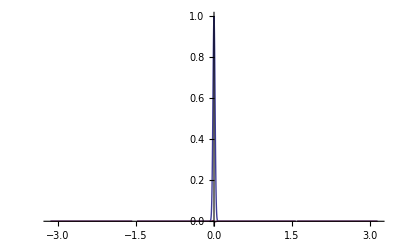

```mathematica
Plot[{Re[g[k,1/5000]],Im[g[k,1/5000]]},{k,-π,π},PlotRange->Full]
```

```mathematica
x1[0,1/100000]
```

-ⅈ (-ⅈ/4+ⅈ/(4 ⅇ^400000))

```mathematica
N[-ⅈ (-ⅈ/4+ⅈ/(4 ⅇ^400000))]
```

-0.25+0. ⅈ

```mathematica
N[-ⅈ (-ⅈ/4+ⅈ/(4 ⅇ^400))]
```

-0.25+0. ⅈ

```mathematica
X1[x_]=Normal[Series[x1[0,x],{x,0,2}]];
X2[x_]=Normal[Series[x2[0,x],{x,0,2}]];
```

```mathematica
meanX[A1_,A2_,B1_,B2_]=Coefficient[X1[1/t],t,0]+Coefficient[X1[1/t],t]*t;
varX[A1_,A2_,B1_,B2_]=Limit[Coefficient[X2[1/t]-meanX[A1,A2,B1,B2]^2,t],t->∞];
```

```mathematica
meanX[A1,A2,B1,B2]
```

-((A1+B2) (B1+B2))/(A1+A2+B1+B2)^2+ⅇ^(-(A1 t)/2-(A2 t)/2-(B1 t)/2-(B2 t)/2-1/2 √((A1+A2+B1+B2)^2) t) ((A1^2 B1 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)+(A1 A2 B1 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)+(A1 B1^2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)-(A1 A2 B2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)-(A2^2 B2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)+(A1 B1 B2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)-(A2 B1 B2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)-(A2 B2^2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 (A1+A2+B1+B2)^2)+(A1 B1 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 √((A1+A2+B1+B2)^2))-(A2 B2 ⅇ^((A1 t)/2+(A2 t)/2+(B1 t)/2+(B2 t)/2+1/2 √((A1+A2+B1+B2)^2) t))/(2 √((A1+A2+B1+B2)^2))) t

```mathematica
FullSimplify[%85]
```

(-(A1+B2) (B1+B2)+(A1+A2+B1+B2) (A1 B1-A2 B2) t)/(A1+A2+B1+B2)^2

$Aborted

```mathematica
varX[A1_,A2_,B1_,B2_]=Limit[Coefficient[X2[1/t]-meanX[A1,A2,B1,B2]^2,t],t->∞];
```

```mathematica
FullSimplify[1/(A1+A2+B1+B2)^3(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))]
```

(A1^3 B1+A2 B2 (A2^2+2 A2 B1+(B1+B2)^2)+A1^2 (2 B1 B2+A2 (2 B1+B2))+A1 (B1 (B1+B2)^2+A2^2 (B1+2 B2)+2 A2 (B1^2+4 B1 B2+B2^2)))/(A1+A2+B1+B2)^3

```mathematica
Simplify[X2[1/t]-X1[1/t]^2]
```

$Aborted

```mathematica
(*meanX[A1_,A2_,B1_,B2_]=Limit[Coefficient[Normal[Series[x1[0],{t,∞,2}]],t],t->∞]*t+
Limit[Coefficient[Normal[Series[x1[0],{t,∞,2}]],t,0],t->∞];*)
```

$Aborted

```mathematica
Simplify[x2[0]]
```

$Aborted

```mathematica
mob[A1_,A2_,B1_,B2_] = Coefficient[meanX[A1,A2,B1,B2],t];
varX[A1_,A2_,B1_,B2_]=FullSimplify[Limit[Coefficient[(x2[0]-x1[0]^2),t],t->∞]]
```

```mathematica
Series[x1[0],{t,∞,1}]
```

$Aborted

```mathematica
Limit[Coefficient[Normal[Series[x1[0],{t,∞,2}]],t],t->∞]*t+
Limit[Coefficient[Normal[Series[x2[0],{t,∞,2}]],t,0],t->∞]
```

$Aborted

```mathematica
R2=Normal[Series[R,{k,0,2}]];
L1[k_]=Normal[Series[L[[1]],{k,0,2}]];
L2[k_]=Normal[Series[L[[2]],{k,0,2}]];

λ2=Normal[Series[λ,{k,0,2}]];
ψ0={1,0};
(*g[k_]=(L2⟦1⟧.ψ0 ⅇ^(t λ2⟦1⟧)+L2⟦2⟧.ψ0 ⅇ^(t λ2⟦2⟧));*)
g[k_]=(L1[-k].ψ0 ⅇ^(t λ2⟦1⟧)+L2[-k].ψ0 ⅇ^(t λ2⟦2⟧));
μ[k_]=-ⅈ D[g[k], {k}];
x2[k_]=-D[D[g[k], {k}], {k}];
(*varX=x2[0]-μ[0]^2;*)
μ[0];
meanX[A1_,A2_,B1_,B2_]=Limit[Coefficient[Normal[Series[μ[0],{t,∞,2}]],t],t->∞]*t+
Limit[Coefficient[Normal[Series[μ[0],{t,∞,2}]],t,0],t->∞];
```